## Eigenvalues of a Spherical Square Well

In this notebook, we compute the eigenvalues En of the potential with V = -V0 for r<R and V=0 for r>R.  The derivation can be found in any graduate and many undergraduate quantum mechanics texts.

## l=0

The l=0 case is quite simple.  Inside the well, the radial function has the form u(r) = A Sin[kp*r], with kp given by

```mathematica
kp:=(√(2 mu (V0+En)))/hbar
```

while outside the well the radial function has the form u(r) = B Exp[-kappa*r], with kappa given by

```mathematica
kappa:=(√(-2 mu En))/hbar
```

In these definitions, V0 > 0 and En < 0, mu is the reduced mass and hbar is Planck's constant divided by 2π.   The eigenvalue condition is found by matching the radial wave function and its derivative (or, equivalently, its logarithmic derivative) at r = R.  This implies that the function f(En):

```mathematica
f[En_]:=kappa/kp+1/Tan[kp R]
```

is zero at eigenvalues En.  We can plot this function to see graphically where the eigenvalues lie and then use FindRoot to get numerical values.

### A specific case

Set the mass and hbar to simple values:

```mathematica
hbar=1; mu=1;
```

Choose a particular square well:

```mathematica
R=1; V0=50;
```

Now plot f[En] in the acceptable range for bound states (-V0 < En < 0):

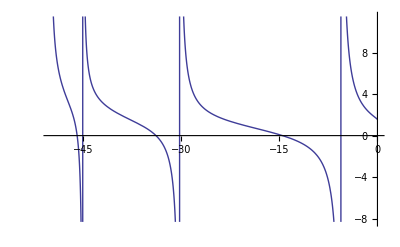

```mathematica
Plot[f[En],{En,-V0,0}]
```

We can see  bound state eigenvalues, near -16 and -6.  (Don't confuse the straight lines Mathematica draws to connect -∞ and +∞ with places where f[En] has a zero.)  Look up FindRoot in the Help Browser to see the possible options.  Here we apply Findroot with a guess AND bounds on where the root is expected (this is one reason to ALWAYS make a plot first):

```mathematica
E1 = En /. FindRoot[f[En],{En,-16,-20,-10}]
```

-14.5248

```mathematica
E2=En /. FindRoot[f[En],{En,-35,-40,-30}]
```

```mathematica
-33.873299403140855
E3=En /. FindRoot[f[En],{En,-46,-48,-42}]
```

-33.8733

-45.9321

If we want a lot of digits, we could try using N[expression, digits]:

```mathematica
N[E1,16]
```

-16.3538

but that doesn't work.  We can verify that these quantities have 16 digits of precision:

```mathematica
Precision[E1]
```

MachinePrecision

Instead of N, use NumberForm:

```mathematica
NumberForm[{E1,E2, E3},16]
```

{-14.52481775693338,-33.87329940314086,-45.93207285858243}

or ScientificForm:

```mathematica
ScientificForm[{E1,E2, E3},16]
```

{-1.452481775693338×10^1,-3.387329940314086×10^1,-4.593207285858243×10^1}